### Categorization

Tutorial

DoFun

DoFun`

DoFun/tutorial/Known issues

### Keywords

Details

# Known issues

This notebook describes known issues of DoFun.

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

## DSEPlot

### Non-planar diagrams

Non-planar diagrams pose a problem for the used plot program GraphPlot as the following example illustrates:

```mathematica
Needs["DoFun`"]
```

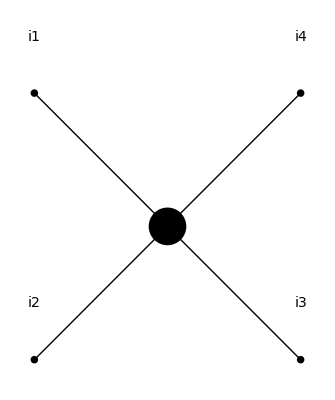
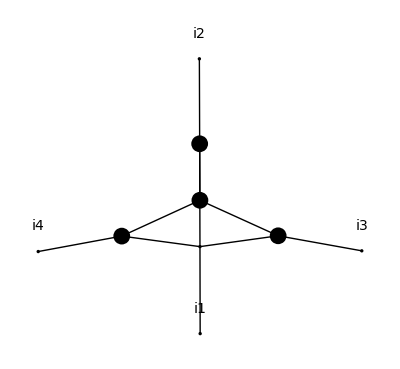
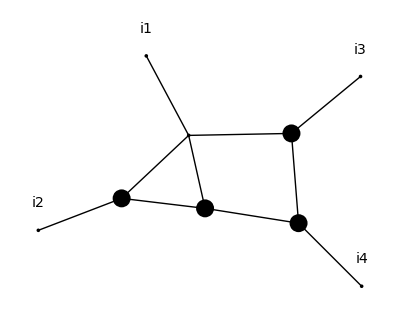
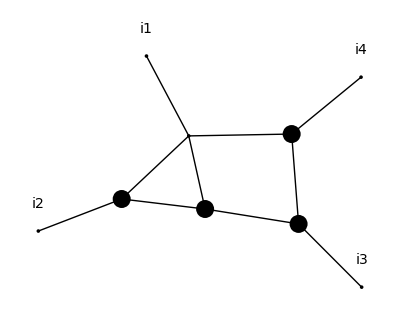
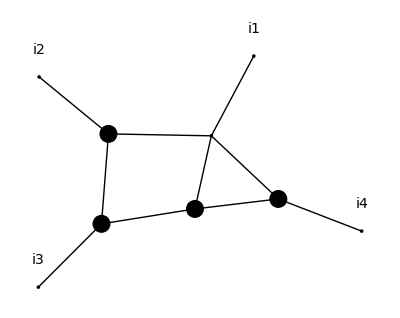
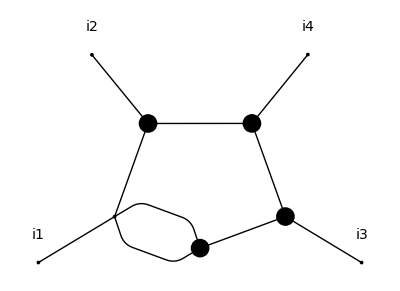
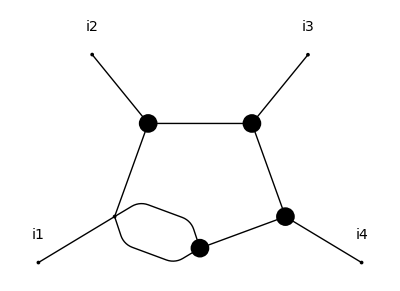
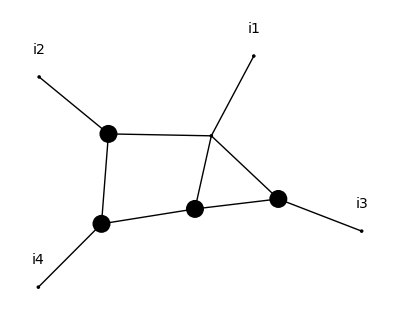
-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+1/2^ |  |  |

```mathematica
dse=doDSE[{{phi,4}},{phi,phi,phi,phi}];
dse=Select[dse,Count[#,P[__],∞]==6&];
DSEPlot[dse,{{phi,Black}}]
```

Clearly the first diagram is drawn in a disadvantageous way, but the output of doDSE is correct.

Similar problems might occur for other graphs.

## doDSE

Actions with n-point functions higher than four-point functions have some diagrams appear several times. However, the coefficients are correct and adding them up yields the expected results. The reason for this problem is that the identification of diagrams no longer works properly in this case.

Here is simple an example:

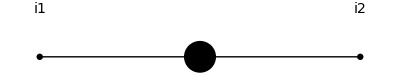
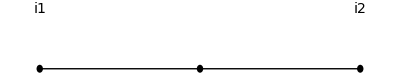
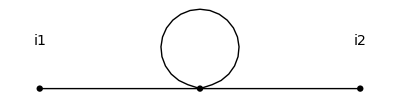
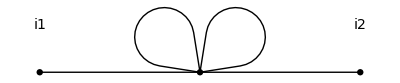
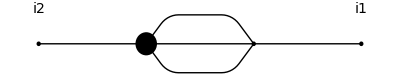
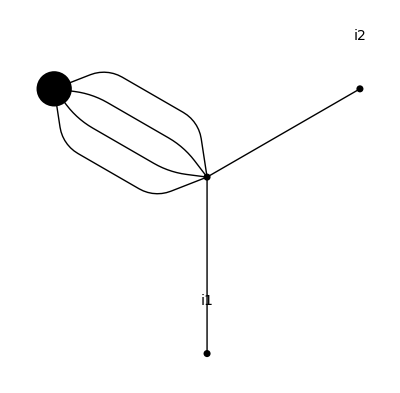
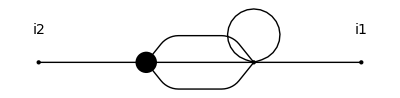
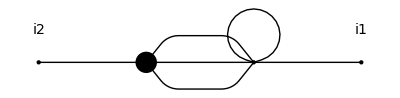
-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/8^ | -Graphics--1/6^
 | -Graphics--1/24^ | -Graphics--1/30^ | -Graphics--1/20^ | -Graphics--1/120^
 | -Graphics--1/40^ | -Graphics--1/40^ | -Graphics--1/30^ |

```mathematica
dse=doDSE[{{phi,6,even}},{phi,phi}];
DSEPlot[dse,{{phi,Black}}]
```

Adding up the 6th and 7th diagrams yields the coefficient 1/12 which is exactly the one expected by the symmetry of the diagram: 3! 2.

The same is true for the 9th, 10th and 11th diagrams: 12=3! 2.

More About

Related Tutorials

Related Wolfram Education Group Courses